### Analysis of CDC Data for the purpose of verifying Google Trends

```mathematica
cdcdata=Import["~/Desktop/BioPhys/flu_project/data_inputs/FluViewPhase2Data/WHO_NREVSS_Combined_prior_to_2015_16.csv"];
Print[cdcdata[[2]]];
cdcdata=cdcdata[[3;;]];
cdcstart="oct-08-1997";
```

{REGION TYPE,REGION,YEAR,WEEK,TOTAL SPECIMENS,PERCENT POSITIVE,A (2009 H1N1),A (H1),A (H3),A (Subtyping not Performed),A (Unable to Subtype),B,H3N2v}

```mathematica
hhsregions=Import["~/Desktop/BioPhys/flu_project/data_inputs/hhsregions.csv"];
hhspolys=Entity["AdministrativeDivision",{#, "UnitedStates"}]["Polygon"]&/@#&/@hhsregions;
```

```mathematica
datetoindex[initialdate_,date_]:=
Return[1+DateDifference[initialdate,date][[1]]];

indextodate[initialdate_,index_]:=
Return[initialdate+Quantity[1, "Days"]*(index-1)];
```

```mathematica
dict[___]=-1;
keys={};
For[i=1,i<Length[cdcdata],i+=1,
date=DateString[DateObject["jan-01-"<>ToString[cdcdata[[i]][[3]]]]+cdcdata[[i]][[4]]Quantity[, "Weeks"]];
If[dict[date]==-1,
AppendTo[keys,date];
dict[date]=0.;,
dict[date]=dict[date]+cdcdata[[i]][[5]]*cdcdata[[i]][[6]]/100.
];
];
nationalcdcdata={DateObject[#],dict[#]}&/@keys;
maxnatcdc=Max[Transpose[nationalcdcdata][[2]]];
minnatcdc=Min[Transpose[nationalcdcdata][[2]]];
```

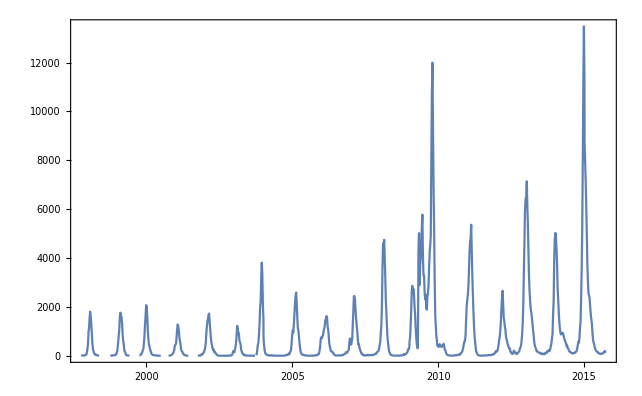

```mathematica
DateListPlot[nationalcdcdata,PlotRange->All]
```

```mathematica
byregion={DateObject["jan-01-"<>ToString[#[[3]]]]+#[[4]]Quantity[, "Weeks"],#[[5]]*#[[6]]/100.}&/@#&/@Table[cdcdata[[i;;;;10]],{i,1,10}]/."X"->0;
ibyregion={datetoindex[cdcstart,#[[1]]],#[[2]]}&/@#&/@byregion;
```

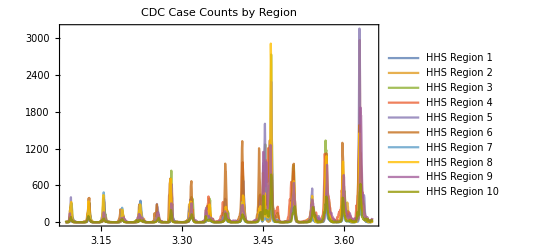

```mathematica
DateListPlot[byregion,PlotRange->All,PlotStyle->Opacity[.8],PlotLabel->"CDC Case Counts by Region",PlotLegends->Table["HHS Region "<>ToString[i],{i,1,10}]]
```

```mathematica
Manipulate[
Module[{f,fdata,interpolation,minsep},
f[i_,j_,s_]:=∑_(t=Max[1,1+Abs[s]])^Min[Length[byregion[[1]]],Length[byregion[[1]]]-Abs[s]] (ibyregion[[i]][[t-s]][[2]]-ibyregion[[j]][[t]][[2]])^2
;
fdata=Table[{s,f[i,j,s]},{s,-25,25}];
interpolation=Interpolation[fdata];
minsep=NMinimize[interpolation[x],{x}];
Grid[{{
GeoListPlot[{hhspolys[[i]],hhspolys[[j]]},GeoRange->"Country",GeoBackground->GeoStyling["ReliefMap"],ImageSize->Small,PlotLegends->("HHS Region: "<>ToString[#]&/@{i,j})]},
{DateListPlot[{byregion[[i]],byregion[[j]]},PlotRange->All,PlotStyle->Opacity[.8],PlotLegends->("HHS Region: "<>ToString[#]&/@{i,j}),ImageSize->Large]},
{Plot[interpolation[s],{s,-25,25},PlotRange->All,ImageSize->Small]},
{Text[If[(x/.minsep[[2]])<=0,"Region "<>ToString[i]<>" was hit "<>ToString[(Round[-x/.minsep[[2]],.01])]<> " weeks after Region "<>ToString[j],"Region "<>ToString[i]<>" was hit "<>ToString[(Round[x/.minsep[[2]],.01])]<> " weeks before Region "<>ToString[j]]]}
},ItemSize->Full,Alignment->{Left,Right},Spacings->{0,0}]
],{{i,1,"Region 1"},Table[j,{j,1,10}],ControlType->SetterBar},{{j,4,"Region 2"},Table[k,{k,1,10}],ControlType->SetterBar}]
```

```mathematica
hhstimeseps=Table[Table[Round[s2/.NMinimize[Interpolation[Table[{s,f[i,j,s]},{s,-10,10}]][s2],{s2}][[2]],.001],{i,1,10}],{j,1,10}];
hhstimeseps=Table[Join[{"HHS "<>ToString[i]},hhstimeseps[[i]]],{i,1,10}];
hhstimeseps=Join[{Join[{"X"},Table["HHS "<>ToString[i],{i,1,10}]]},hhstimeseps];
```

```mathematica
Grid[hhstimeseps,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
```

X | HHS 1 | HHS 2 | HHS 3 | HHS 4 | HHS 5 | HHS 6 | HHS 7 | HHS 8 | HHS 9 | HHS 10
HHS 1 | 0. | 0.058 | 1.358 | 3.647 | 2.386 | 3.42 | 2.649 | 2.741 | 0.509 | 1.962
HHS 2 | -0.058 | 0. | 0.806 | 2.549 | 1.92 | 2.774 | 2.195 | 2.327 | -0.431 | 1.549
HHS 3 | -1.358 | -0.806 | 0. | 1.23 | 0.737 | 2. | 1. | 0.977 | -1.138 | -0.136
HHS 4 | -3.646 | -2.549 | -1.23 | 0. | 0.055 | 0.406 | -0.192 | -0.917 | -3.495 | -2.248
HHS 5 | -2.386 | -1.92 | -0.737 | -0.055 | 0. | 0.949 | 0.292 | 0.364 | -3.691 | -0.883
HHS 6 | -3.42 | -2.774 | -2. | -0.405 | -0.949 | 0. | -0.712 | -1.04 | -3. | -1.714
HHS 7 | -2.649 | -2.195 | -1. | 0.193 | -0.291 | 0.712 | 0. | 0.007 | -1.717 | -1.067
HHS 8 | -2.741 | -2.327 | -0.977 | 0.917 | -0.364 | 1.04 | -0.007 | 0. | -1.809 | -1.014
HHS 9 | -0.507 | 0.433 | 1.139 | 3.495 | 3.691 | 3. | 1.72 | 1.809 | 0. | 0.542
HHS 10 | -1.961 | -1.548 | 0.136 | 2.247 | 0.883 | 1.714 | 1.067 | 1.014 | -0.54 | 0.